# Exercise sheet 3

José Alfredo de León

## Definitions

```mathematica
MatrixForm[H=1/(√2){{1,1},{1,-1}}]
MatrixForm[M0=Outer[Times,{1,0},{1,0}]]
MatrixForm[M1=Outer[Times,{0,1},{0,1}]]

MatrixForm[CX={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

(1 | 0
0 | 0)

(0 | 0
0 | 1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

## Exercise 1 (Hadamard test)

```mathematica
(H.M0.H+H.M1.H).{1,0}
```

{1,0}

## Exercise 3

```mathematica
(*Define CNOT(0,1), CNOT(1,0) and Swap*)
MatrixForm[CNOT0=KroneckerProduct[M0,IdentityMatrix[2]]+KroneckerProduct[M1,Pauli[1]]]
MatrixForm[CNOT1=KroneckerProduct[IdentityMatrix[2],M0]+KroneckerProduct[Pauli[1],M1]]
MatrixForm[Swap={{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(*Do matrix multiplication*)
MatrixForm[CNOT0.CNOT1.CNOT0]
CNOT0.CNOT1.CNOT0==Swap
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

True

## Exercise 12

```mathematica
PurityDepOutputState[n_,p_,L_]:=p^(2L)+(1-p^(2L))/2^(2n)
```

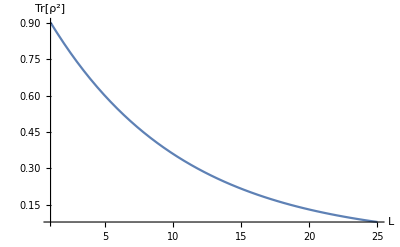

```mathematica
Plot[PurityDepOutputState[5,0.95,L],{L,1,25},PlotRange->Full,AxesLabel->{L,Tr[ρ^2]}]
```

```mathematica
(-6.91- -6.92)/-6.91
```

-0.00144718

```mathematica
0.05/6.95
```

0.00719424